```mathematica
SetDirectory[NotebookDirectory[]];
```

{{a→κ,b→κ/(κ+μ)}}

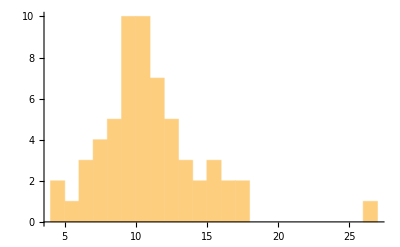

10.5

```mathematica
Clear[μ,κ,a,b]
size = 60;
Solve[{(a (1-b))/b==μ,(a (1-b))/b^2==μ + ((μ^2)/κ)},{a,b}]
μ = 10;
κ = 20;
a = κ;
b = κ/(κ+μ);
realData=RandomVariate[NegativeBinomialDistribution[a,b],{size}];
Histogram[realData,20]
xbar = N@Mean@realData
```

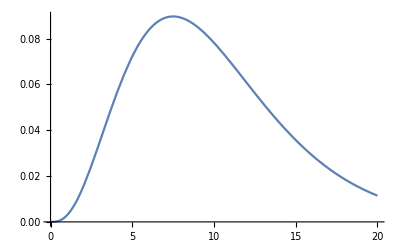

```mathematica
α = 4;
β = 0.4;
Plot[PDF[GammaDistribution[α,1/β],x],{x,0,20}]
```

```mathematica
Mean@GammaDistribution[size*xbar + α,1/(β+size)]
```

10.4967

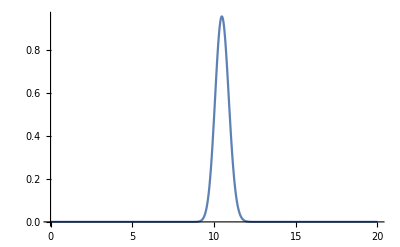

```mathematica
Plot[PDF[GammaDistribution[size*xbar + α,1/(β+size)],x],{x,0,20},PlotRange->Full]
```

```mathematica
pDataPois=Integrate[PDF[GammaDistribution[α,1/β],λ]*Likelihood[PoissonDistribution[λ],realData],{λ,0,∞}]
```

4.13568×10^-71

```mathematica
pDataNB=NIntegrate[PDF[GammaDistribution[α,1/β],m]*PDF[BetaDistribution[1,1],m/(m+n)]*Likelihood[NegativeBinomialDistribution[m,m/(m+n)],realData],{m,0,∞},{n,0,∞}]
```

1.05088×10^-70

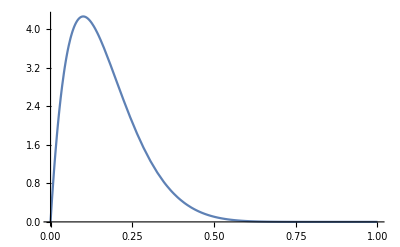

```mathematica
Plot[PDF[BetaDistribution[2,10],p],{p,0,1}]
```

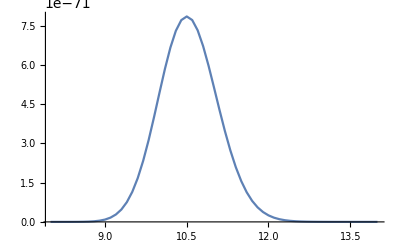

```mathematica
ListLinePlot[Table[{r,NIntegrate[PDF[GammaDistribution[α,1/β],m]*PDF[BetaDistribution[1,1],m/(m+r)]*Likelihood[NegativeBinomialDistribution[m,m/(m+r)],realData],{m,0,∞}]},{r,8,14,0.1}]]
```

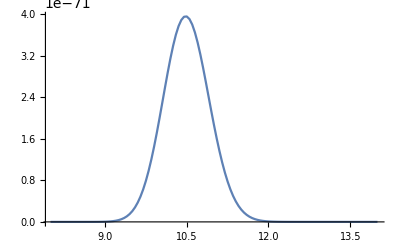

```mathematica
ListLinePlot[Table[{r,PDF[GammaDistribution[α,1/β],r]*Likelihood[PoissonDistribution[r],realData]},{r,8,14,0.05}]]
```

```mathematica
dataNB=Table[{r,NIntegrate[PDF[GammaDistribution[α,1/β],m]*PDF[BetaDistribution[1,1],m/(m+r)]*Likelihood[NegativeBinomialDistribution[m,m/(m+r)],realData],{m,0,∞}]},{r,8,14,0.05}];
```

```mathematica
dataPois=Table[{r,PDF[GammaDistribution[α,1/β],r]*Likelihood[PoissonDistribution[r],realData]},{r,8,14,0.05}];
```

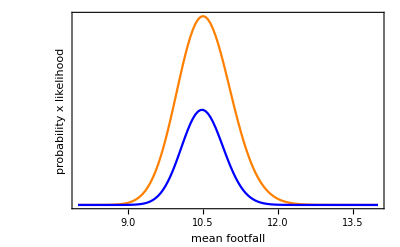

```mathematica
gBF=Show[ListLinePlot[dataNB,PlotStyle->Orange,PlotLegends->Placed[{"negative binomial"},{0.76,0.5}]],ListLinePlot[dataPois,PlotStyle->Blue,PlotLegends->Placed[{"poisson"},{0.76,0.5}]],Frame->{True,True,False,False},FrameTicks->{True,False},FrameLabel->{"mean footfall","probability x likelihood"},BaseStyle->{FontSize->14}]
```

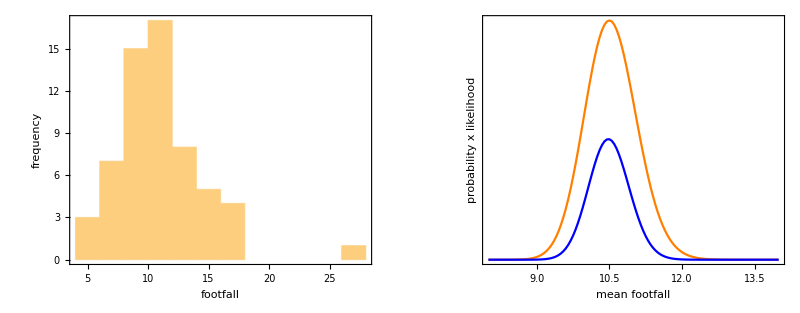

```mathematica
gFinal=Show[GraphicsRow[{Show[Histogram[realData,Frame->{True,True,False,False}],FrameLabel->{"footfall","frequency"},BaseStyle->{FontSize->14}],gBF}],ImageSize->800]
```

```mathematica
Export["Posterior_modelComparisonFootfall.pdf",gFinal]
```

Posterior_modelComparisonFootfall.pdf

```mathematica
pDataNB/pDataPois
```

2.54101